# Изпит-Задача 4-Георги Г.-2001261019

търсим общо решение

```mathematica
Clear[x, y]
DSolve[y'[x] ==y[x] - 2Sin[x], y[x], x]
```

{{y[x]→ⅇ^x C[1]+Cos[x]+Sin[x]}}

търсим частно решение

```mathematica
Clear[x, y,yt]
DSolve[{y'[x] ==y[x] - 2Sin[x], y[0] == 9}, y[x], x]
```

{{y[x]→8 ⅇ^x+Cos[x]+Sin[x]}}

```mathematica
yt[x_]:= 8 ⅇ^x+ Cos[x]+Sin[x]
```

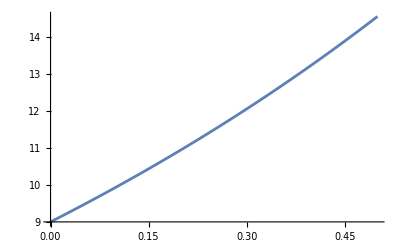

```mathematica
Plot[yt[x], {x, 0,0.5}]
```

Мрежата е с n = 13 и стъпка h = 0.0384615

Теоретичната локална грешка  е 0.00147929

Теоретичната глобална грешка е 0.0384615

i = 0 x_i = 0. y_i = 9. f_i = 9. y_точно = 9. Истинска грешка = 0.

i = 1 x_i = 0.0384615 y_i = 9.34615 f_i = 9.26925 y_точно = 9.3514 Истинска грешка = 0.00524472

i = 2 x_i = 0.0769231 y_i = 9.70266 f_i = 9.54897 y_точно = 9.71356 Истинска грешка = 0.0108987

i = 3 x_i = 0.115385 y_i = 10.0699 f_i = 9.83967 y_точно = 10.0869 Истинска грешка = 0.0169879

i = 4 x_i = 0.153846 y_i = 10.4484 f_i = 10.1419 y_точно = 10.4719 Истинска грешка = 0.02354

i = 5 x_i = 0.192308 y_i = 10.8385 f_i = 10.4562 y_точно = 10.869 Истинска грешка = 0.0305839

i = 6 x_i = 0.230769 y_i = 11.2406 f_i = 10.7832 y_точно = 11.2788 Истинска грешка = 0.0381502

i = 7 x_i = 0.269231 y_i = 11.6554 f_i = 11.1234 y_точно = 11.7016 Истинска грешка = 0.0462709

i = 8 x_i = 0.307692 y_i = 12.0832 f_i = 11.4775 y_точно = 12.1382 Истинска грешка = 0.0549798

i = 9 x_i = 0.346154 y_i = 12.5246 f_i = 11.8461 y_точно = 12.5889 Истинска грешка = 0.0643127

i = 10 x_i = 0.384615 y_i = 12.9802 f_i = 12.2298 y_точно = 13.0545 Истинска грешка = 0.0743068

i = 11 x_i = 0.423077 y_i = 13.4506 f_i = 12.6295 y_точно = 13.5356 Истинска грешка = 0.0850017

i = 12 x_i = 0.461538 y_i = 13.9364 f_i = 13.0457 y_точно = 14.0328 Истинска грешка = 0.0964386

i = 13 x_i = 0.5 y_i = 14.4381 f_i = 13.4793 y_точно = 14.5468 Истинска грешка = 0.108661

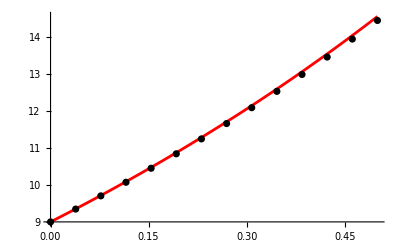

```mathematica
(*Въвеждаме услонието на задачата*)
a = 0.;b=0.5;
x = a;
y =9.;
points = {{x,y}};
f[x_,y_] := y - 2Sin[x]
(*Точно решение*)
yt[x_] := 8 ⅇ^x+ Cos[x]+Sin[x]
(*Съставяме мрежата*)
n = 13; h = (b - a)/n;
Print["Мрежата е с n = ", n , " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална грешка  е ", h^2]
Print["Теоретичната глобална грешка е ", h]
(*Намираме неизвестните стойности за Subscript[y, i]*)
For[i = 0, i  <= n, i++,
Print["i = ", i, " x_i = ", x, " y_i = ", y, " f_i = ", f[x,y] , " y_(:0442:043e:0447:043d:043e) = ", yt[x], " Истинска грешка = ", Abs[y-yt[x]]];
y = y + h*f[x,y];
x = x + h;
AppendTo[points, {x,y}]
]
(*Визуализация на резултатите*)
gryt = Plot[yt[x], {x, a, b}, PlotStyle->Red];
grp = ListPlot[points, PlotStyle->Black];
Show[gryt, grp]
```

Мрежата е с n = 13 и стъпка h = 0.0384615

Теоретичната локална грешка  е 0.0000568958

Теоретичната глобална грешка е 0.00147929

i = 0 x_i = 0. y_i = 9. f_i = 9. x_(i + 1/2) = 0.0192308 y_(i + 1/2) = 9.17308 f_(i + 1/2) = 9.13462  y_точно = 9. Истинска грешка = 0.

i = 1 x_i = 0.0384615 y_i = 9.35133 f_i = 9.27443 x_(i + 1/2) = 0.0576923 y_(i + 1/2) = 9.52969 f_(i + 1/2) = 9.41437  y_точно = 9.3514 Истинска грешка = 0.0000671142

i = 2 x_i = 0.0769231 y_i = 9.71342 f_i = 9.55973 x_(i + 1/2) = 0.0961538 y_(i + 1/2) = 9.89726 f_(i + 1/2) = 9.70525  y_точно = 9.71356 Истинска грешка = 0.000139691

i = 3 x_i = 0.115385 y_i = 10.0867 f_i = 9.85644 x_(i + 1/2) = 0.134615 y_(i + 1/2) = 10.2762 f_(i + 1/2) = 10.0078  y_точно = 10.0869 Истинска грешка = 0.000218076

i = 4 x_i = 0.153846 y_i = 10.4716 f_i = 10.1651 x_(i + 1/2) = 0.173077 y_(i + 1/2) = 10.6671 f_(i + 1/2) = 10.3227  y_точно = 10.4719 Истинска грешка = 0.000302635

i = 5 x_i = 0.192308 y_i = 10.8686 f_i = 10.4864 x_(i + 1/2) = 0.211538 y_(i + 1/2) = 11.0703 f_(i + 1/2) = 10.6504  y_точно = 10.869 Истинска грешка = 0.000393751

i = 6 x_i = 0.230769 y_i = 11.2783 f_i = 10.8208 x_(i + 1/2) = 0.25 y_(i + 1/2) = 11.4864 f_(i + 1/2) = 10.9916  y_точно = 11.2788 Истинска грешка = 0.000491828

i = 7 x_i = 0.269231 y_i = 11.701 f_i = 11.169 x_(i + 1/2) = 0.288462 y_(i + 1/2) = 11.9158 f_(i + 1/2) = 11.3469  y_точно = 11.7016 Истинска грешка = 0.000597293

i = 8 x_i = 0.307692 y_i = 12.1374 f_i = 11.5317 x_(i + 1/2) = 0.326923 y_(i + 1/2) = 12.3592 f_(i + 1/2) = 11.7169  y_точно = 12.1382 Истинска грешка = 0.000710591

i = 9 x_i = 0.346154 y_i = 12.5881 f_i = 11.9095 x_(i + 1/2) = 0.365385 y_(i + 1/2) = 12.8171 f_(i + 1/2) = 12.1025  y_точно = 12.5889 Истинска грешка = 0.000832194

i = 10 x_i = 0.384615 y_i = 13.0536 f_i = 12.3032 x_(i + 1/2) = 0.403846 y_(i + 1/2) = 13.2902 f_(i + 1/2) = 12.5043  y_точно = 13.0545 Истинска грешка = 0.000962598

i = 11 x_i = 0.423077 y_i = 13.5345 f_i = 12.7134 x_(i + 1/2) = 0.442308 y_(i + 1/2) = 13.779 f_(i + 1/2) = 12.9229  y_точно = 13.5356 Истинска грешка = 0.00110232

i = 12 x_i = 0.461538 y_i = 14.0315 f_i = 13.1409 x_(i + 1/2) = 0.480769 y_(i + 1/2) = 14.2843 f_(i + 1/2) = 13.3593  y_точно = 14.0328 Истинска грешка = 0.00125191

i = 13 x_i = 0.5 y_i = 14.5454 f_i = 13.5865 x_(i + 1/2) = 0.519231 y_(i + 1/2) = 14.8066 f_(i + 1/2) = 13.8142  y_точно = 14.5468 Истинска грешка = 0.00141195

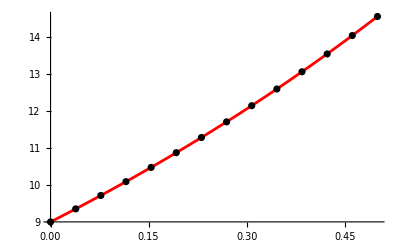

```mathematica
(*Въвеждаме услонието на задачата*)
a = 0.;b=0.5;
x = a;
y =9.;
points = {{x,y}};
f[x_,y_] := y - 2Sin[x]
(*Точно решение*)
yt[x_] := 8 ⅇ^x+ Cos[x]+Sin[x]
(*Съставяме мрежата*)
n = 13; h = (b - a)/n;
Print["Мрежата е с n = ", n , " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална грешка  е ", h^3]
Print["Теоретичната глобална грешка е ", h^2]
(*Намираме неизвестните стойности за Subscript[y, i]*)
For[i = 0, i  <= n, i++,
x12 = x + h/2;
y12 = y + h/2 f[x,y];
Print["i = ", i, " x_i = ", x, " y_i = ", y, " f_i = ", f[x,y]  , " x_(i + 1/2) = ", x12, " y_(i + 1/2) = ", y12, " f_(i + 1/2) = ", f[x12,y12]  " y_(:0442:043e:0447:043d:043e) = ", yt[x], " Истинска грешка = ", Abs[y-yt[x]]];
y = y + h*f[x12,y12];
x = x + h;
AppendTo[points, {x,y}]
]
(*Визуализация на резултатите*)
gryt = Plot[yt[x], {x, a,b}, PlotStyle->Red];
grp = ListPlot[points, PlotStyle-> Black];
Show[gryt, grp]
```